```mathematica
Clear["Global`*"]
$PlotTheme="Scientific";
```

```mathematica
PositivePart[x_]:=If[x>=0,x,0];
R = {x, y, z};
$Assumptions = x ∈ Reals && y ∈ Reals && z ∈ Reals && ρ ∈ Reals && ρ > 0 && θ ∈ Reals && ϕ ∈ Reals && k ∈ Reals && k > 0 && ω > 0;
r = Sqrt[R . R];
predecessor[α_] := If[α == {0, 0, 0},
   {0, 0, 0},
   Select[
     Table[α - UnitVector[3, j], {j, 1, 3}],
     NonNegative@Min@# &,
     1
     ][[1]]
   ];
firstNonzeroDim[α_] := Position[
     α,
     _?(# > 0 &),
     Infinity, 1
     ][[1]][[1]];
g[α_,direction_] := If[α == {0, 0, 0},
   1/4/π/r,
   Block[{j, α1, ga},
    α1 = α;
    j = firstNonzeroDim[α];
    α1[[j]] = α1[[j]] - 1;
    ga = g[α1,direction];
    D[ga, R[[j]]] -direction ⅉ k R[[j]]/r ga // Expand
    ]
   ]
h[α_,direction_,farField_] := Exp[-direction ⅉ k r] If[farField&&Norm[α,1]>0,
k^Norm[α,1]Coefficient[g[α,direction],k^Norm[α,1]],
g[α,direction]];
μ = k^2/ω^2/ϵ;
c = 1/Sqrt[μ ϵ] // Simplify;
SimplifiedHeaviside[x_] := If[x >= 0, 1, 0];
SafeMoment[CurrentMoment_,α_,dim_]:=If[AllTrue[α,#>=0&],
CurrentMoment[α,dim],
0];
ChargeMoment[α_, CurrentMoment_, dim_,direction_] := -1/(direction ⅉ ω) Sum[If[dim == j,
    α[[j]] SimplifiedHeaviside[α[[j]] - 2] (α[[j]] - 1) SafeMoment[CurrentMoment,(α[[j]] - 2) UnitVector[3, j] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {j }]], j],
    α[[j]] α[[dim]] SimplifiedHeaviside[α[[j]] - 1] SimplifiedHeaviside[α[[dim]] - 1] SafeMoment[CurrentMoment,(α[[j]] - 1) UnitVector[3, j] + (α[[dim]] - 1) UnitVector[3, dim] + Total[α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {dim, j}]], j]
    ],
   {j, 1, 3}]
ElectricMoment[α_, CurrentMoment_, dim_,direction_] :=direction μ ⅉ ω CurrentMoment[α, dim] + 1/ϵ ChargeMoment[α, CurrentMoment, dim,direction]
MagneticMoment[α_,CurrentMoment_, dim_,direction_] := -direction μ Sum[LeviCivitaTensor[3][[dim]][[i]][[j]] SimplifiedHeaviside[α[[i]] - 1] α[[i]] CurrentMoment[(α[[i]] - 1) UnitVector[3, i] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {i}]], j],
   {i, 1, 3}, {j, 1, 3}]
Field[α_, CurrentMoment_, MomentFunction_, dim_,direction_,farField_] := Block[{β},
β=(-1)^Norm[α, 1]/(Times @@ (Factorial/@ α)) MomentFunction[α, CurrentMoment, dim,direction];
If[β===0||β===0.,
0,
β h[α,direction,farField]
]
]
ElectricField[α_, CurrentMoment_, dim_,direction_,farField_] := Field[α, CurrentMoment, ElectricMoment, dim,direction,farField];
MagneticField[α_, CurrentMoment_, dim_,direction_,farField_] := Field[α, CurrentMoment, MagneticMoment, dim,direction,farField];
On[Assert]
CurrentMoment[α_, dim_] := If[α == {0, 0, 0} && dim == 3,
  ⅉ ω p, 0]
EfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,-1,False],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}];
BfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[MagneticField[{ax, ay, az}, CurrentMoment, dim,-1,False],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}];
P = {0, 0, p};
n = R/r;
HJackson = TransformedField["Cartesian" -> "Spherical",
    c k^2/4/π n×P Exp[ⅉ k r]/r (1 - 1/ⅉ/k/r),
    R -> {ρ, θ, ϕ}] // Simplify;
EJackson = TransformedField["Cartesian" -> "Spherical",
    1/4/π/ϵ Exp[ⅉ k r] (k^2/r (n×P)×n + (3 n (n . P) - P) (1/r^3 - ⅉ k/r^2)),
    R -> {ρ, θ, ϕ}] // Simplify;
Assert[Simplify[BfieldThis - HJackson μ] == {0, 0, 0}]
Assert[Simplify[EfieldThis - EJackson] == {0, 0, 0}]
Clear[CurrentMoment, EfieldThis, BfieldThis, P, n, HJackson, EJackson]
```

```mathematica
Outer[Block[{},
mk=#1;
nk=#2;

d0=1; (* Base unit of length *)
t0=1*^-8; (* Base unit of time *)

n=12;
L=4/10/d0;
a=12/1000/d0;
d=a(n-1)/d0;
kp=π Sqrt[mk^2 +nk^2]/d;
k0=If[kp==0,0,Select[Flatten@Values@Solve[Cos[x L/2]-x/kp==0,x,Reals],#>0&,1][[1]]];
Print[N@k0];
indices=Range[1,n];
x0s=Subdivide[-d/2,d/2,n-1];
y0s=Subdivide[-d/2,d/2,n-1];

(*Assert[EvenQ@n];
FourierA=Table[DiscreteDelta[i-mk]DiscreteDelta[j-nk],
{i,1,n},{j,1,n}];
A=Re@InverseFourier[FourierA];*)
A=Sin[mk π/d (x0s-d/2)]⊗Sin[nk π/d (y0s-d/2)];
FourierA=Fourier[A];

c0=3*^8/d0 t0;
λ0=2π/k0;
f0=c0/λ0;
ωn=2π f0;
ϵ0=1*^-6;

Print@Ceiling[Sqrt[(L/2)^2+(d/2)^2]/λ0 16];

maxOrder=2;
zIntegrals=Association@Table[n->NIntegrate[Cos[k0 z]If[n==0,1,z^n],{z,-L/2,L/2}],
{n,0,maxOrder+2}];
FieldFunctions={ElectricField,MagneticField};
(*CurrentMoment[α_, dim_] :=If[dim==3&&Norm[α,1]<=maxOrder-2,
Total@Flatten@Outer[A[[#1,#2]]zIntegrals[α[[3]]]If[α[[1]]==0,1,x0s[[#1]]^α[[1]]]If[α[[2]]==0,1,y0s[[#2]]^α[[2]]]&,
indices,indices],
0
];
fields=ParallelTable[
Sum[
FieldFunctions[[fieldType]][{ax, ay, az}, CurrentMoment, dim,1,False],
{ax,0,maxOrder},
{ay,0,PositivePart[maxOrder-ax]},
{az,0,PositivePart[maxOrder-ax-ay]}
],
{fieldType,1,2},
{dim,1,3}];*)
CurrentMoment[α_, dim_] :=If[dim==3&&Norm[α,1]<=maxOrder-2,
zIntegrals[α[[3]]]If[α[[1]]==0,1,0]If[α[[2]]==0,1,0],
0
];
fields=ParallelTable[
Sum[
FieldFunctions[[fieldType]][
{ax, ay, az},CurrentMoment[#1,#2]&,
 dim,1,False],
{ax,0,maxOrder},
{ay,0,PositivePart[maxOrder-ax]},
{az,0,PositivePart[maxOrder-ax-ay]}
],
{fieldType,1,2},
{dim,1,3}
];
Efield=Sum[
A[[i,j]]fields[[1,;;]]/.x->x-x0s[[i]]/.y->y-y0s[[j]],
{i,1,n},{j,1,n}
];
Bfield=Sum[
A[[i,j]]fields[[2,;;]]/.x->x-x0s[[i]]/.y->y-y0s[[j]],
{i,1,n},{j,1,n}
];
S=Efield×Conjugate[Bfield]/μ;
angularPlot=1/2Re[S/.ω->ωn/.ϵ->ϵ0/.k->k0/.x->ρ Cos[ϕ]Sin[θ]/.y->ρ Sin[ϕ]Sin[θ]/.z->ρ Cos[θ]/.
ρ^2 Cos[θ]^2+ρ^2 Cos[ϕ]^2 Sin[θ]^2+ρ^2 Sin[θ]^2 Sin[ϕ]^2->ρ^2/.ρ->10λ0];
angularPlot=angularPlot.angularPlot;
g1=ContourPlot[angularPlot,{ϕ,0,2π},{θ,0,π},FrameLabel->{ϕ,θ},ImageSize->Medium,PlotLabel->{#1,#2},PlotRange->All];
(*plotData=Association@Flatten[Table[{ax,ay,az}->Abs@CurrentMoment[{ax,ay,az},3],
{ax,0,maxOrder},{ay,0,PositivePart[maxOrder-ax]},{az,0,PositivePart[maxOrder-ax-ay]}],2];
plotData=Select[plotData,Not[#===0.||#===0]&];
plotData=(plotData-Min@plotData)/(Max@plotData-Min@plotData);
g2=ListPointPlot3D[Keys@plotData,AxesLabel->{Subscript[α, x],Subscript[α, y],Subscript[α, z]},ColorFunction->Function[{x,y,z},
ColorData["TemperatureMap"][
Block[{key},
key={Round[x (maxOrder)],Round[y (maxOrder)],Round[z (maxOrder)]};
If[KeyExistsQ[plotData,key],
plotData[key],
0]
]
]
]
];
GraphicsGrid[{{g1,g2}},ImageSize->Full]*)
g1
]&,{4,5},{4,5}]
```

7.5726

5

$Aborted

357.244

5

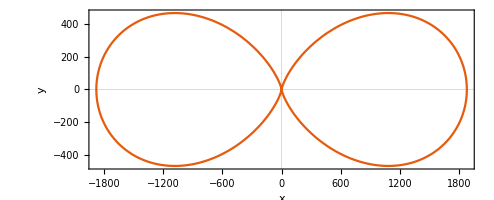

```mathematica
Outer[Block[{},
mk=#1;
nk=#2;

d0=1; (* Base unit of length *)
t0=1*^-8; (* Base unit of time *)

n=14;
L=4/10/d0;
a=12/1000/d0;
d=a(n-1)/d0;
kp=π Sqrt[mk^2 +nk^2]/d;
k0=If[kp==0,0,Select[Flatten@Values@Solve[Cos[x L/2]-x/kp==0,x,Reals],#>0&,1][[1]]];
Print[N[k0/2/π 3*^2]];
indices=Range[1,n];
x0s=Subdivide[-d/2,d/2,n-1];
y0s=Subdivide[-d/2,d/2,n-1];

(*Assert[EvenQ@n];
FourierA=Table[DiscreteDelta[i-mk]DiscreteDelta[j-nk],
{i,1,n},{j,1,n}];
A=Re@InverseFourier[FourierA];*)
A=Cos[mk π/d (x0s-d/2)]⊗Cos[nk π/d ( y0s-d/2)];
FourierA=Fourier[A];

c0=3*^8/d0 t0;
λ0=2π/k0;
f0=c0/λ0;
ωn=2π f0;
ϵ0=1*^-6;

Print@Ceiling[Sqrt[(L/2)^2+(d/2)^2]/λ0 16];

maxOrder=7;
zIntegrals=Association@Table[n->NIntegrate[Cos[k0 z]If[n==0,1,z^n],{z,-L/2,L/2}],
{n,0,maxOrder+2}];
FieldFunctions={ElectricField,MagneticField};
CurrentMoment[α_, dim_] :=If[dim==3&&Norm[α,1]<=maxOrder-2,
Total@Flatten@Outer[A[[#1,#2]]zIntegrals[α[[3]]]If[α[[1]]==0,1,x0s[[#1]]^α[[1]]]If[α[[2]]==0,1,y0s[[#2]]^α[[2]]]&,
indices,indices],
0
];
fields=Table[
Sum[
FieldFunctions[[fieldType]][{ax, ay, az}, CurrentMoment, dim,1,True],
{ax,0,maxOrder},
{ay,0,PositivePart[maxOrder-ax]},
{az,0,PositivePart[maxOrder-ax-ay]}
],
{fieldType,1,2},
{dim,1,3}];
Efield=fields[[1,;;]];
Bfield=fields[[2,;;]];
S=Efield×Conjugate[Bfield]/μ;
angularPlot=1/2Re[S/.ω->ωn/.ϵ->ϵ0/.k->k0/.x->ρ Cos[ϕ]Sin[θ]/.y->ρ Sin[ϕ]Sin[θ]/.z->ρ Cos[θ]/.
ρ^2 Cos[θ]^2+ρ^2 Cos[ϕ]^2 Sin[θ]^2+ρ^2 Sin[θ]^2 Sin[ϕ]^2->ρ^2/.ρ->10λ0];
angularPlot=angularPlot.angularPlot;
g1=ContourPlot[angularPlot,{ϕ,0,2π},{θ,0,π},FrameLabel->{ϕ,θ},ImageSize->Medium,PlotLabel->{#1,#2},PlotRange->All];
(*plotData=Association@Flatten[Table[{ax,ay,az}->Abs@CurrentMoment[{ax,ay,az},3],
{ax,0,maxOrder},{ay,0,PositivePart[maxOrder-ax]},{az,0,PositivePart[maxOrder-ax-ay]}],2];
plotData=Select[plotData,Not[#===0.||#===0]&];
plotData=(plotData-Min@plotData)/(Max@plotData-Min@plotData);
g2=ListPointPlot3D[Keys@plotData,AxesLabel->{Subscript[α, x],Subscript[α, y],Subscript[α, z]},ColorFunction->Function[{x,y,z},
ColorData["TemperatureMap"][
Block[{key},
key={Round[x (maxOrder)],Round[y (maxOrder)],Round[z (maxOrder)]};
If[KeyExistsQ[plotData,key],
plotData[key],
0]
]
]
]
];
GraphicsGrid[{{g1,g2}},ImageSize->Full]*)
PolarPlot[
angularPlot/.θ->π/2,{ϕ,0,2π},
FrameLabel->{x,y}
]
(*g1*)
]&,{3}, {4}]
```

357.244

5

357.244

5

357.244

5

357.244

5

357.244

5

357.244

5

357.244

5

357.244

5

357.244

5

357.244

5

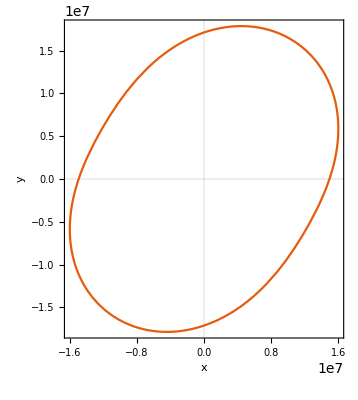
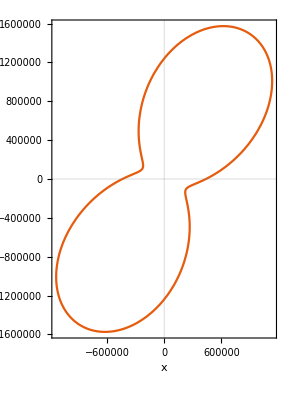
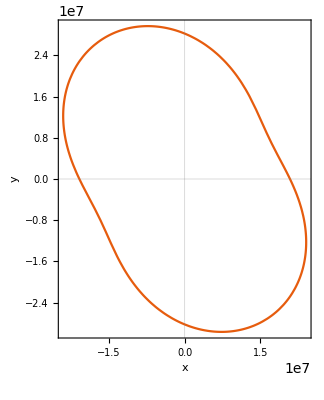
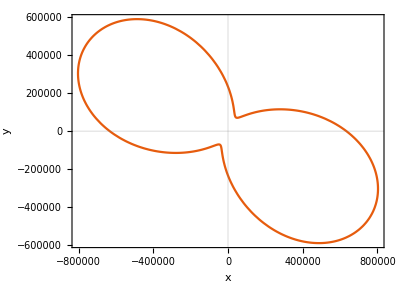
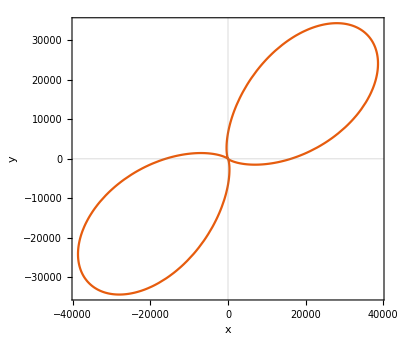
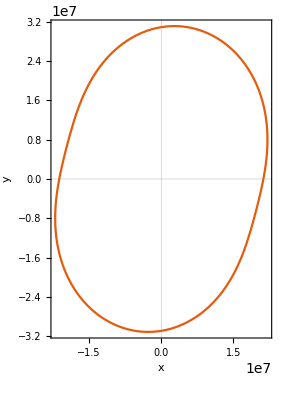
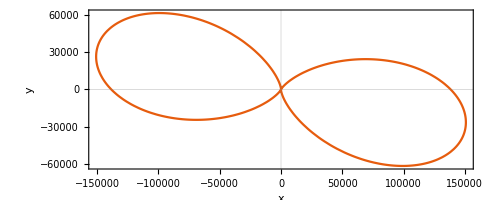
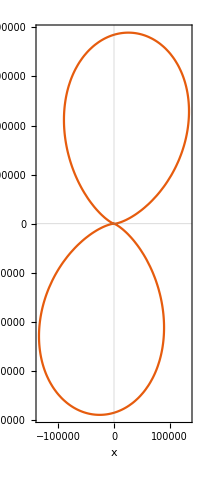

```mathematica
Table[Block[{},
d0=1; (* Base unit of length *)
t0=1*^-8; (* Base unit of time *)

n=14;
L=4/10/d0;
a=12/1000/d0;
d=a(n-1)/d0;
kp=π Sqrt[mk^2 +nk^2]/d;
k0=If[kp==0,0,Select[Flatten@Values@Solve[Cos[x L/2]-x/kp==0,x,Reals],#>0&,1][[1]]];
Print[N[k0/2/π 3*^2]];
indices=Range[1,n];
x0s=Subdivide[-d/2,d/2,n-1];
y0s=Subdivide[-d/2,d/2,n-1];

(*Assert[EvenQ@n];
FourierA=Table[DiscreteDelta[i-mk]DiscreteDelta[j-nk],
{i,1,n},{j,1,n}];
A=Re@InverseFourier[FourierA];*)
A=RandomReal[{-1,1},{n,n}];

c0=3*^8/d0 t0;
λ0=2π/k0;
f0=c0/λ0;
ωn=2π f0;
ϵ0=1*^-6;

Print@Ceiling[Sqrt[(L/2)^2+(d/2)^2]/λ0 16];

maxOrder=7;
zIntegrals=Association@Table[n->NIntegrate[Cos[k0 z]If[n==0,1,z^n],{z,-L/2,L/2}],
{n,0,maxOrder+2}];
FieldFunctions={ElectricField,MagneticField};
CurrentMoment[α_, dim_] :=If[dim==3&&Norm[α,1]<=maxOrder-2,
Total@Flatten@Outer[A[[#1,#2]]zIntegrals[α[[3]]]If[α[[1]]==0,1,x0s[[#1]]^α[[1]]]If[α[[2]]==0,1,y0s[[#2]]^α[[2]]]&,
indices,indices],
0
];
fields=Table[
Sum[
FieldFunctions[[fieldType]][{ax, ay, az}, CurrentMoment, dim,1,True],
{ax,0,maxOrder},
{ay,0,PositivePart[maxOrder-ax]},
{az,0,PositivePart[maxOrder-ax-ay]}
],
{fieldType,1,2},
{dim,1,3}];
Efield=fields[[1,;;]];
Bfield=fields[[2,;;]];
S=Efield×Conjugate[Bfield]/μ;
angularPlot=1/2Re[S/.ω->ωn/.ϵ->ϵ0/.k->k0/.x->ρ Cos[ϕ]Sin[θ]/.y->ρ Sin[ϕ]Sin[θ]/.z->ρ Cos[θ]/.
ρ^2 Cos[θ]^2+ρ^2 Cos[ϕ]^2 Sin[θ]^2+ρ^2 Sin[θ]^2 Sin[ϕ]^2->ρ^2/.ρ->10λ0];
angularPlot=angularPlot.angularPlot;
g1=ContourPlot[angularPlot,{ϕ,0,2π},{θ,0,π},FrameLabel->{ϕ,θ},ImageSize->Medium,PlotLabel->{#1,#2},PlotRange->All];
(*plotData=Association@Flatten[Table[{ax,ay,az}->Abs@CurrentMoment[{ax,ay,az},3],
{ax,0,maxOrder},{ay,0,PositivePart[maxOrder-ax]},{az,0,PositivePart[maxOrder-ax-ay]}],2];
plotData=Select[plotData,Not[#===0.||#===0]&];
plotData=(plotData-Min@plotData)/(Max@plotData-Min@plotData);
g2=ListPointPlot3D[Keys@plotData,AxesLabel->{Subscript[α, x],Subscript[α, y],Subscript[α, z]},ColorFunction->Function[{x,y,z},
ColorData["TemperatureMap"][
Block[{key},
key={Round[x (maxOrder)],Round[y (maxOrder)],Round[z (maxOrder)]};
If[KeyExistsQ[plotData,key],
plotData[key],
0]
]
]
]
];
GraphicsGrid[{{g1,g2}},ImageSize->Full]*)
PolarPlot[
angularPlot/.θ->π/2,{ϕ,0,2π},
FrameLabel->{x,y}
]
(*g1*)
],{iteration,1,10}]
```

```mathematica
Sort[Association@Flatten[Table[{ax,ay,az}->Abs@CurrentMoment[{ax,ay,az},3],
{ax,0,maxOrder},{ay,0,PositivePart[maxOrder-ax]},{az,0,PositivePart[maxOrder-ax-ay]}]],
Abs@#1>=Abs@#2&]
```

<|{0,0,0}→4.72071,{0,1,0}→0.0690985,{0,0,2}→0.0389821,{1,0,0}→0.0198,{2,0,0}→0.0152554,{0,2,0}→0.0100841,{1,1,0}→0.00273286,{0,0,4}→0.000701524,{0,1,2}→0.000570593,{1,0,2}→0.000163502,{2,1,0}→0.000150241,{2,0,2}→0.000125974,{0,3,0}→0.000114375,{1,2,0}→0.000093834,{0,2,2}→0.0000832717,{4,0,0}→0.0000678847,{0,4,0}→0.0000375045,{2,2,0}→0.0000349179,{3,0,0}→0.0000294362,{1,1,2}→0.0000225671,{3,1,0}→0.0000132863,{0,1,4}→0.0000102684,{1,3,0}→3.72206×10^-6,{1,0,4}→2.9424×10^-6,{3,2,0}→1.40958×10^-6,{2,1,2}→1.24064×10^-6,{2,3,0}→1.1692×10^-6,{4,1,0}→9.82747×10^-7,{0,3,2}→9.44471×10^-7,{1,4,0}→9.42496×10^-7,{1,2,2}→7.74852×10^-7,{3,0,2}→2.43075×10^-7,{5,0,0}→2.40788×10^-7,{0,5,0}→1.25991×10^-7,{0,0,1}→0.,{0,0,3}→0.,{0,0,5}→0.,{0,0,6}→0,{0,0,7}→0,{0,1,1}→0.,{0,1,3}→0.,{0,1,5}→0,{0,1,6}→0,{0,2,1}→0.,{0,2,3}→0.,{0,2,4}→0,{0,2,5}→0,{0,3,1}→0.,{0,3,3}→0,{0,3,4}→0,{0,4,1}→0.,{0,4,2}→0,{0,4,3}→0,{0,5,1}→0,{0,5,2}→0,{0,6,0}→0,{0,6,1}→0,{0,7,0}→0,{1,0,1}→0.,{1,0,3}→0.,{1,0,5}→0,{1,0,6}→0,{1,1,1}→0.,{1,1,3}→0.,{1,1,4}→0,{1,1,5}→0,{1,2,1}→0.,{1,2,3}→0,{1,2,4}→0,{1,3,1}→0.,{1,3,2}→0,{1,3,3}→0,{1,4,1}→0,{1,4,2}→0,{1,5,0}→0,{1,5,1}→0,{1,6,0}→0,{2,0,1}→0.,{2,0,3}→0.,{2,0,4}→0,{2,0,5}→0,{2,1,1}→0.,{2,1,3}→0,{2,1,4}→0,{2,2,1}→0.,{2,2,2}→0,{2,2,3}→0,{2,3,1}→0,{2,3,2}→0,{2,4,0}→0,{2,4,1}→0,{2,5,0}→0,{3,0,1}→0.,{3,0,3}→0,{3,0,4}→0,{3,1,1}→0.,{3,1,2}→0,{3,1,3}→0,{3,2,1}→0,{3,2,2}→0,{3,3,0}→0,{3,3,1}→0,{3,4,0}→0,{4,0,1}→0.,{4,0,2}→0,{4,0,3}→0,{4,1,1}→0,{4,1,2}→0,{4,2,0}→0,{4,2,1}→0,{4,3,0}→0,{5,0,1}→0,{5,0,2}→0,{5,1,0}→0,{5,1,1}→0,{5,2,0}→0,{6,0,0}→0,{6,0,1}→0,{6,1,0}→0,{7,0,0}→0|>

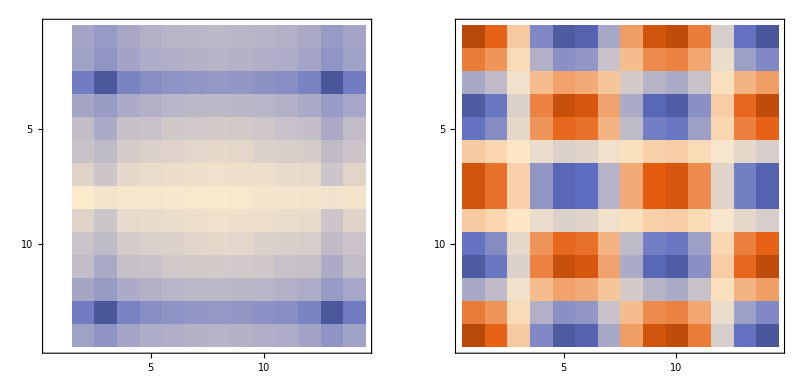

```mathematica
mk=3;nk=4;
A=Cos[mk π/d (x0s-d/2)]⊗Cos[nk π/d ( y0s-d/2)];
FourierA=Fourier[A];
GraphicsGrid[{{
MatrixPlot[Transpose@Abs@FourierA],
MatrixPlot[Transpose@A]
}},ImageSize->Full]
```

```mathematica
FarFieldPattern[α_,dim_]:=Block[{CurrentMoment,Efield,Bfield,S,plot,maxOrder,ρ},
maxOrder=Norm[α,1]+2;
CurrentMoment=Function[{β,dim2},If[dim2==dim&&α==β,1,0]];
Efield=Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim2,1,True],
      {ax, 0, maxOrder}, {ay, 0, PositivePart[maxOrder - ax]}, {az, 0, PositivePart[maxOrder - ax - ay]}],
{dim2,1,3}];
Bfield=Table[Sum[MagneticField[{ax, ay, az}, CurrentMoment, dim2,1,True],
      {ax, 0, maxOrder}, {ay, 0,PositivePart[ maxOrder - ax]}, {az, 0, PositivePart[maxOrder - ax - ay]}],
{dim2,1,3}];
S=Efield×Conjugate[Bfield];
plot=S/.ω->2π/.ϵ->1/.k->2π/.x->Cos[ϕ]Sin[θ]/.y->Sin[ϕ]Sin[θ]/.z->Cos[θ];
plot=Re[plot.plot];
SphericalPlot3D[plot,{θ,0,Pi},{ϕ,0,2π},ImageSize->Medium,
Axes->False,Boxed->False,(*PlotLabel->α,AxesLabel->{x,y,z},*)
Mesh->False,
PlotRange->Full,
ViewPoint->{1,1,1}
]
];
order=2;
Graphics3D[Flatten@Table[
Inset[FarFieldPattern[{ax,ay,order-ax-ay},3],{ax,ay,order-ax-ay},Automatic,50,None],
{ax,0,order},{ay,0,PositivePart[order-ax]}
],
Axes->True,
AxesLabel->{x,y,z},
ViewPoint->{1,1,1}
]
```

-Graphics3D-

```mathematica
order=2;
(*Table[
SphericalPlot3D[
Im[SphericalBesselJ[l,1]SphericalHarmonicY[l,m,θ,ϕ]],
{θ,0,π},{ϕ,0,2π},
PlotLabel->{l,m}
],
{l,0,2},{m,-l,l}
]*)
SphericalPlot3D[
Re[(
h[{1,1,0},1,True]
)/.k->1/.x->Cos[ϕ]Sin[θ]/.y->Sin[ϕ]Sin[θ]/.z->Cos[θ]],
{θ,0,π},{ϕ,0,2π}
]
```

-Graphics3D-

```mathematica
field=Expand@Simplify@TransformedField[
"Cartesian"->"Spherical",
D[SphericalHankelH2[1,r]LegendreP[1,Cos[ArcTan[z,√(x^2+y^2)]]],y],
R->{ρ,θ,ϕ}];
field
SphericalHarmonicY[2,1,θ,ϕ]+SphericalHarmonicY[2,-1,θ,ϕ]//ExpToTrig
LegendreP[2,1,Cos[θ]]Sin[ϕ]//Simplify
```

1/4 Sin[2 θ] Sin[ϕ] SphericalHankelH2[0,ρ]-(3 Sin[2 θ] Sin[ϕ] SphericalHankelH2[1,ρ])/(4 ρ)-1/4 Sin[2 θ] Sin[ϕ] SphericalHankelH2[2,ρ]

-ⅈ √(15/(2 π)) Cos[θ] Sin[θ] Sin[ϕ]

-3 Abs[Sin[θ]] Cos[θ] Sin[ϕ]

```mathematica
α={2,0,0};
h200=Expand@ExpToTrig@Simplify@TransformedField["Cartesian"->"Spherical",
ⅇ^(ⅈ ρ)h[α,1,False],
R->{ρ,θ,ϕ}
]/.k->1;
maxL=Norm[α,1];
sphericalHarmonics=Expand@Sum[ExpToTrig@Expand@FunctionExpand[
Subscript[f, l,m] SphericalHarmonicY[l,m,θ,ϕ]ⅇ^(ⅈ ρ)SphericalHankelH2[l,ρ]
],
{l,0,maxL},{m,-l,l}
];
eqn=TrigExpand[h200==sphericalHarmonics]/.ρ->1/ρ/.Cos[θ]->cθ/.Sin[θ]->sθ/.Cos[ϕ]->cϕ/.Sin[ϕ]->sϕ;
SolveAlways[eqn,{ρ,cθ,sθ,cϕ,sϕ}]
```

{{f_(0,0)→ⅈ/(6 √π),f_(1,0)→0,f_(1,-1)→0,f_(1,1)→0,f_(2,-1)→0,f_(2,1)→0,f_(2,-2)→-ⅈ/(2 √(30 π)),f_(2,2)→-ⅈ/(2 √(30 π)),f_(2,0)→ⅈ/(6 √(5 π))}}

```mathematica
ParallelTable[{l,m}->
Integrate[(
CoefficientList[g[{1,0,1},1],k]/.k->1/.x->Cos[ϕ]Sin[θ]/.y->Sin[ϕ]Sin[θ]/.z->Cos[θ]//Simplify)Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]Sin[θ],
{θ,0,π},{ϕ,0,2π}
],
{l,0,2},{m,-l,l}
]
```

{{{0,0}→{0,0,0}},{{1,-1}→{0,0,0},{1,0}→{0,0,0},{1,1}→{0,0,0}},{{2,-2}→{0,0,0},{2,-1}→{1/2 √(3/(10 π)),1/2 ⅈ √(3/(10 π)),-1/(2 √(30 π))},{2,0}→{0,0,0},{2,1}→{-1/2 √(3/(10 π)),-1/2 ⅈ √(3/(10 π)),1/(2 √(30 π))},{2,2}→{0,0,0}}}

```mathematica
FarFieldPower[α_,dim_]:=Block[{CurrentMoment,Efield,Bfield,S,plot,maxOrder,ρ,useFarField},
maxOrder=Norm[α,1]+2;
useFarField=True;
CurrentMoment=Function[{β,dim2},If[dim2==dim&&α==β,1,0]];
Efield=Table[Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim2,1,useFarField],
      {ax, 0, maxOrder}, {ay, 0, PositivePart[maxOrder - ax]}, {az, 0, PositivePart[maxOrder - ax - ay]}],
{dim2,1,3}];
Bfield=Table[Sum[MagneticField[{ax, ay, az}, CurrentMoment, dim2,1,useFarField],
      {ax, 0, maxOrder}, {ay, 0,PositivePart[ maxOrder - ax]}, {az, 0, PositivePart[maxOrder - ax - ay]}],
{dim2,1,3}];
S=Efield×Conjugate[Bfield];
plot=Re[S/.ω->2π/.ϵ->1/.k->2π/.x->ρ Cos[ϕ]Sin[θ]/.y->ρ Sin[ϕ]Sin[θ]/.z->ρ Cos[θ]]/.ρ->10;
plot=plot.plot;
NIntegrate[plot Sin[θ],{θ,0,π},{ϕ,0,2π},WorkingPrecision->12]
];
Show[
ParallelTable[
Block[{data},
If[order==0,
ListPointPlot3D[{{0,0,FarFieldPower[{0,0,0},3]}},
ColorFunction->"SouthwestColors"],
data=Association@Table[{ax,ay}->
FarFieldPower[{ax,ay,order-ax-ay},3],
{ax,order,Floor[order/2],-1},{ay,0,PositivePart[order-ax]}
];
ListPlot3D[
KeyValueMap[{#1[[1]],#1[[2]],Log10@#2}&,data],
Mesh->None,InterpolationOrder->1,ColorFunction->"SouthwestColors",
PlotRange->{{0,order},{0,order/2},Automatic},PlotLegends->{Subscript[α, x],Subscript[α, y],_}]
]
],
{order,10,0,-1}],
ImageSize->Large]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

-Graphics3D-

```mathematica
Table[Sum[1,
{ax,0,l},{ay,0,PositivePart[l-ax]}],
{l,0,100}]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820,861,903,946,990,1035,1081,1128,1176,1225,1275,1326,1378,1431,1485,1540,1596,1653,1711,1770,1830,1891,1953,2016,2080,2145,2211,2278,2346,2415,2485,2556,2628,2701,2775,2850,2926,3003,3081,3160,3240,3321,3403,3486,3570,3655,3741,3828,3916,4005,4095,4186,4278,4371,4465,4560,4656,4753,4851,4950,5050,5151}

```mathematica
SphericalPlot3D[
angularPlot,
{θ,0,π},{ϕ,0,2π},ImageSize->Medium,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
plotLimit=2λ0;
PlotFunction=Identity;
plotDim=1;
plotExpression=E;
plotExpression=plotExpression/.ω->ωn/.ϵ->ϵ0/.k->k0;
plotExpression=plotExpression HeavisideTheta[x^2+y^2+z^2-1.1(L^2+d^2/4)];
plotExpression={plotExpression.Conjugate[plotExpression]};
plotXY=PlotFunction[plotExpression[[plotDim]]/.z->0];
plotXZ=PlotFunction[plotExpression[[plotDim]]/.y->0];
plotYZ=PlotFunction[plotExpression[[plotDim]]/.x->0];

plotMin=2*^6;
plotMax=2*^4;

colorFunction=ColorData[{"M10DefaultDensityGradient",{plotMin,plotMax}}];
GraphicsGrid[{{
ContourPlot[plotXY,{x,-plotLimit,plotLimit},{y,-plotLimit,plotLimit},PlotLegends->Automatic
(*, ColorFunction->colorFunction,ColorFunctionScaling->False*)],
ContourPlot[plotXZ,{x,-plotLimit,plotLimit},{z,-plotLimit,plotLimit},PlotLegends->Automatic(*,ColorFunction->colorFunction,ColorFunctionScaling->False*)],
ContourPlot[plotYZ,{y,-plotLimit,plotLimit},{z,-plotLimit,plotLimit},PlotLegends->Automatic(*,ColorFunction->colorFunction,ColorFunctionScaling->False*)]
}},ImageSize->Full]
(*To3D[plot_,height_,opacity_,direction_]:=Module[{newplot},
newplot=First@Graphics[plot];
newplot=N@newplot/. {x_?AtomQ,y_?AtomQ}->Switch[direction,
1,{height,x,y},
2,{x,height,y},
3,{x,y,height},
_,{x,y,height}];
newplot/. GraphicsComplex[xx__]->{Opacity[opacity],GraphicsComplex[xx]}];
opacity=1;
Graphics3D[{
To3D[ContourPlot[plotXY,{x,-plotLimit,plotLimit},{y,-plotLimit,plotLimit},ColorFunction->colorFunction,ColorFunctionScaling->False],-0,opacity,3],
To3D[ContourPlot[plotXZ,{x,-plotLimit,plotLimit},{z,-plotLimit,plotLimit},ColorFunction->colorFunction,ColorFunctionScaling->False],-0,opacity,2],
To3D[ContourPlot[plotYZ,{y,-plotLimit,plotLimit},{z,-plotLimit,plotLimit},ColorFunction->colorFunction,ColorFunctionScaling->False],-0,opacity,1]
},Lighting->AmbientLight[White],Axes->True,AxesLabel->{x,y,z},ImageSize->Medium]*)
```

-Graphics-

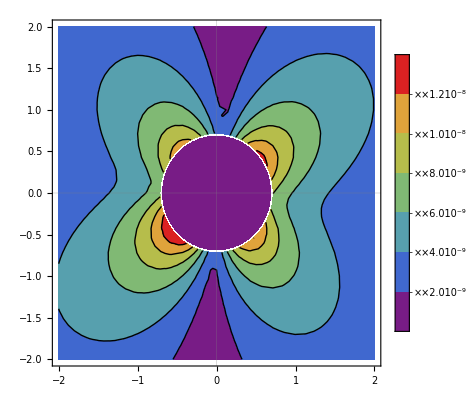

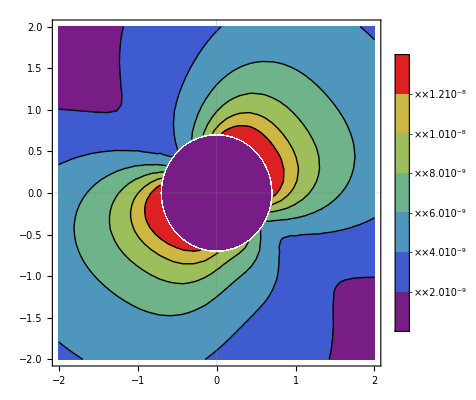

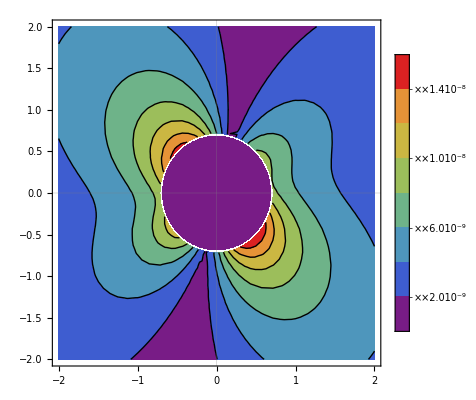

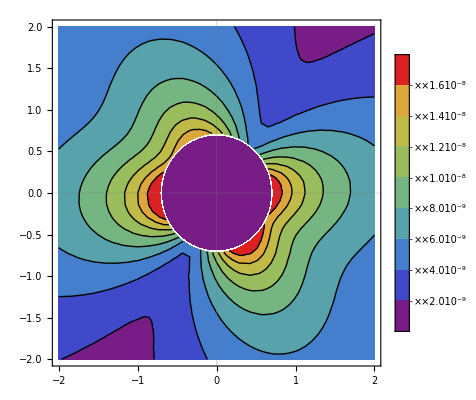

```mathematica
xs={1,-3,-5,7}/100;
ys={2,4,-6,-8}/100;
sign={1,-1,1,-1};
CurrentMoment=Function[{α,dim},If[dim==3&&α[[3]]==0,
Sum[
sign[[i]]*xs[[i]]^α[[1]]ys[[i]]^α[[2]],
{i,1,4}
],
0]];
quadrupoleTensor={
{CurrentMoment[{2,0,0},3],CurrentMoment[{1,1,0},3],0},
{CurrentMoment[{1,1,0},3],CurrentMoment[{0,2,0},3],0},
{0,0,0}
};
quadrupoleTensorTrace=Tr[quadrupoleTensor]/3IdentityMatrix[3];
quadrupoleTensorDetrace=quadrupoleTensor-quadrupoleTensorTrace;
Assert[Tr[quadrupoleTensorDetrace]==0]
tensorUsed=quadrupoleTensorDetrace;
CurrentMomentDetrace=Function[{α,dim},
If[Norm[α,1]==2,
Switch[α,
{2,0,0},tensorUsed[[1,1]],
{1,1,0},tensorUsed[[2,1]],
{0,2,0},tensorUsed[[2,2]],
_,0
],
CurrentMoment[α,dim]]
];
maxOrderJxx=4;
EfieldDetrace=Table[
Sum[
ElectricField[{ax, ay, az}, CurrentMomentDetrace,dim,1,False],
{ax, 0, maxOrderJxx}, {ay, 0, PositivePart[maxOrderJxx - ax]}, {az, 0, PositivePart[maxOrderJxx - ax - ay]}],
{dim,3,3}]/.z->0/.ϵ->1/.ω->2π 1*^9/.k->2π/3*^8*1*^9;
tensorUsed=3quadrupoleTensorTrace;
CurrentMomentDetrace=Function[{α,dim},
If[Norm[α,1]==2,
Switch[α,
{2,0,0},tensorUsed[[1,1]],
{1,1,0},tensorUsed[[2,1]],
{0,2,0},tensorUsed[[2,2]],
_,0
],
CurrentMoment[α,dim]]
];
maxOrderJxx=4;
EfieldTrace=Table[
Sum[
ElectricField[{ax, ay, az}, CurrentMomentDetrace,dim,1,False],
{ax, 0, maxOrderJxx}, {ay, 0, PositivePart[maxOrderJxx - ax]}, {az, 0, PositivePart[maxOrderJxx - ax - ay]}],
{dim,3,3}]/.z->0/.ϵ->1/.ω->2π 1*^9/.k->2π/3*^8*1*^9;
tensorUsed=quadrupoleTensor;
CurrentMomentDetrace=Function[{α,dim},
If[Norm[α,1]==2,
Switch[α,
{2,0,0},tensorUsed[[1,1]],
{1,1,0},tensorUsed[[2,1]],
{0,2,0},tensorUsed[[2,2]],
_,0
],
CurrentMoment[α,dim]]
];
maxOrderJxx=4;
Efield=Table[
Sum[
ElectricField[{ax, ay, az}, CurrentMomentDetrace,dim,1,False],
{ax, 0, maxOrderJxx}, {ay, 0, PositivePart[maxOrderJxx - ax]}, {az, 0, PositivePart[maxOrderJxx - ax - ay]}],
{dim,3,3}]/.z->0/.ϵ->1/.ω->2π 1*^9/.k->2π/3*^8*1*^9;
ContourPlot[Abs@EfieldDetrace*HeavisideTheta[x^2+y^2-.7^2],{x,-2,2},{y,-2,2},PlotLegends->Automatic,ColorFunction->ColorData["Rainbow"]]
ContourPlot[Abs@EfieldTrace*HeavisideTheta[x^2+y^2-.7^2],{x,-2,2},{y,-2,2},PlotLegends->Automatic,ColorFunction->ColorData["Rainbow"]]
ContourPlot[Abs@Efield*HeavisideTheta[x^2+y^2-.7^2],{x,-2,2},{y,-2,2},PlotLegends->Automatic,ColorFunction->ColorData["Rainbow"]]
ContourPlot[Abs[EfieldDetrace+EfieldTrace]*HeavisideTheta[x^2+y^2-.7^2],{x,-2,2},{y,-2,2},PlotLegends->Automatic,ColorFunction->ColorData["Rainbow"]]
```

```mathematica
Table[
{ax,2-ax}->N@CurrentMoment[{ax,2-ax,0},3],
{ax,0,2}]
```

{{0,2}→-0.004,{1,1}→0.01,{2,0}→-0.0032}

```mathematica
F=1/2;
Table[{ax,ay,az}->
Integrate[
((1-λ)F)^ax(λ/Sqrt[2])^(ay+az)+((1-λ)F)^ax(-λ/Sqrt[2])^ay(λ/Sqrt[2])^az-(((1-λ)F)^ax(λ/Sqrt[2])^ay(-λ/Sqrt[2])^az+((1-λ)F)^ax(-λ/Sqrt[2])^ay(-λ/Sqrt[2])^az),
{λ,0,1}],
{ax,0,lMax},{ay,0,lMax-ax},{az,0,lMax-ax-ay}
]//N
```

{{{{0.,0.,0.}→0.,{0.,0.,1.}→1.41421,{0.,0.,2.}→0.,{0.,0.,3.}→0.353553},{{0.,1.,0.}→0.,{0.,1.,1.}→0.,{0.,1.,2.}→0.},{{0.,2.,0.}→0.,{0.,2.,1.}→0.353553},{{0.,3.,0.}→0.}},{{{1.,0.,0.}→0.,{1.,0.,1.}→0.235702,{1.,0.,2.}→0.},{{1.,1.,0.}→0.,{1.,1.,1.}→0.},{{1.,2.,0.}→0.}},{{{2.,0.,0.}→0.,{2.,0.,1.}→0.0589256},{{2.,1.,0.}→0.}},{{{3.,0.,0.}→0.}}}